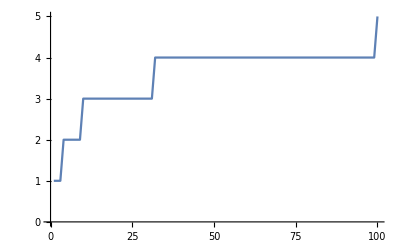

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

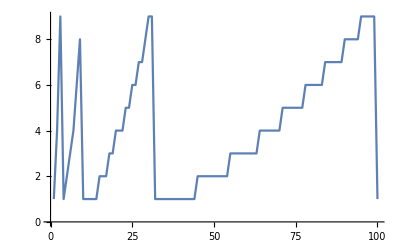

{0,4,18,48,100,180,294,448,648,900}

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

{4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000}

{-3,-2,-1,0,1,2}

{1
1
1,2
4
8,3
9
27,4
16
64,5
25
125,6
36
216,7
49
343,8
64
512,9
81
729,10
100
1000,11
121
1331,12
144
1728,13
169
2197,14
196
2744,15
225
3375,16
256
4096,17
289
4913,18
324
5832,19
361
6859,20
400
8000}

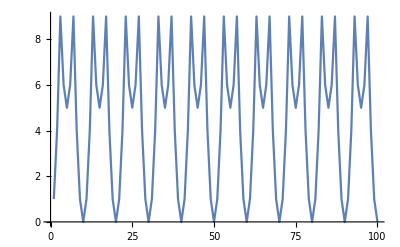

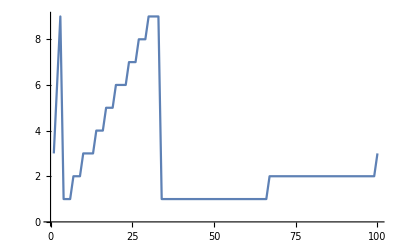

```mathematica
(* 6.1 *)
Table[1000, 5];
(* 6.2 *)
Table[n^3, {n, 10, 20}];
(* 6.3 *)
NumberLinePlot[Table[n^2, {n, 20}]];
(* 6.4 *)
Table[2*n, {n, 1, 10}];
(* 6.5 *)
Table[n, {n, 1, 10}] == Range[10];
(* 6.6 *)
BarChart[Table[n^2, {n, 10}], ImageSize->Small];
(* 6.7 *)
Table[IntegerDigits[n^2], {n, 10}];
(* 6.8 *)
ListLinePlot[Table[Length[IntegerDigits[n^2]], {n, 100}]]
(* 6.9 *)
Table[First[IntegerDigits[n^2]], {n, 20}]
(* 6.10 *)
ListLinePlot[Table[First[IntegerDigits[n^2]], {n, 100}]]
(* +6.1 *)
Table[n^3 - n^2, {n, 10}]
(* +6.2 *)
Table[n, {n, 1, 100, 2}]
(* +6.3 *)
Table[n^2,{n,2,100,2}]
(* +6.4 *)
Range[-3, 2]
(* +6.5 *)
Table[Column[{n, n^2, n^3}] ,{n, 20}]
(* +6.6 *)
ListLinePlot[Table[Last[IntegerDigits[n^2]], {n, 100}]]
(* +6.7 *)
ListLinePlot[Table[First[IntegerDigits[n*3]], {n, 100}]]
```